```mathematica
(*w=1*)
q[v_]:=0.5*Erfc[v/(√2)];
(*Int*)
gTmp1[x_, b_, k_, beta_, ns_, w_]:=beta-x/w(k+b-(1-beta/ns)w x);
gTmp2[x_, b_, k_, beta_, ns_, w_]:=k+b-(1-beta/ns)w x;
(*gTmp1[x_, b_, k_, beta_, ns_, w_]:=beta-x/w(k+b-w x);
gTmp2[x_, b_, k_, beta_, ns_, w_]:=k+b-w x;*)
g1Int[b_, k_, nd_, ns_, ndR_, beta_, w_]:=NIntegrate[gTmp1[x, b, k, beta, ns, w] Exp[-x^2/2]/(√(2.π))Sum[Binomial[nd-1, m-1] q[x]^(m-1)(1-q[x])^(nd-m), {m, 1, ndR}], {x, -Infinity, k+b}];
g21Int[b_, k_, nd_, ns_, ndR_, beta_, w_]:=NIntegrate[gTmp2[x, b, k, beta, ns, w]^2 Exp[-x^2/2.]/(√(2.π))Sum[Binomial[nd-1, m-1] q[x]^(m-1)(1-q[x])^(nd-m), {m, 1, ndR}], {x, -Infinity, k+b}];
g22Int[b_, k_, nd_, ns_, ndR_, beta_, w_]:=NIntegrate[(gTmp1[x, b, k, beta, ns, w]^2-gTmp2[x, b, k, beta, ns, w]^2/w^2) Exp[-x^2/2]/(√(2.π))Sum[Binomial[nd-1, m-1] q[x]^(m-1)(1-q[x])^(nd-m), {m, 1, ndR}], {x, -Infinity, k+b}];
g31Int[b_, k_, nd_, ns_, ndR_, beta_, w_]:=NIntegrate[3gTmp1[x, b, k, beta, ns, w] gTmp2[x, b, k, beta, ns, w]^2 Exp[-x^2/2]/(√(2.π))Sum[Binomial[nd-1, m-1] q[x]^(m-1)(1-q[x])^(nd-m), {m, 1, ndR}], {x, -Infinity, k+b}];
g32Int[b_, k_, nd_, ns_, ndR_, beta_, w_]:=NIntegrate[(gTmp1[x, b, k, beta, ns, w]^3-(3gTmp1[x, b, k, beta, ns, w] gTmp2[x, b, k, beta, ns, w]^2)/w^2) Exp[-x^2/2]/(√(2.π))Sum[Binomial[nd-1, m-1] q[x]^(m-1)(1-q[x])^(nd-m), {m, 1, ndR}], {x, -Infinity, k+b}];
betaSolution[b_, k_, nd_, ns_, ndR_, w_]:=y/.FindRoot[g21Int[b, k, nd, ns, ndR, y, w]-2g1Int[b, k, nd, ns, ndR, y, w]+g22Int[b, k, nd, ns, ndR, y, w]/ns , {y, 0.0, 100.}, Method->"Brent"];
getSkewNormalParam[ns_,  beta_, gsList_, u0_, t_]:=Module[{g1, g21, g31, g32, m1, m2, m3, tmp, mu, sigma, alpha}, 
{g1, g21, g31, g32}=gsList;
m1 = u0 Exp[-g1 t/ns];
m2 = 1.+(u0^2 -1)Exp[-g21 t/ns];
m3=(3.g21-g31/ns)/(3g21-4g1+g32/ns^2)u0 Exp[-g1 t/ns]+(u0^3-(3.g21-g31/ns)/(3g21-4g1+g32/ns^2)u0)Exp[-(3g21-3g1+g32/ns^2)/ns t];
tmp=Sign[m3-3m1 m2 +2 m1^3] √(π/2.)(Abs[2/(4-π)(m3-3m1 m2 +2 m1^3)])^(1/3);
mu=m1-√(2./π) tmp;
sigma =√(m2-m1^2+2./π tmp^2);
alpha = √(tmp^2/(sigma^2-tmp^2))Sign[tmp];
{mu, sigma, alpha}

];
getNormalParam[ns_,  beta_, gsList_, u0_, t_]:=Module[{g1, g21, g31, g32, m1, m2, mu, sigma}, 
{g1, g21, g31, g32}=gsList;
m1 = u0 Exp[-g1 t/ns];
m2 = 1.+(u0^2 -1)Exp[-g21 t/ns];
mu=m1;
sigma=√(m2-m1^2);
{mu, sigma}
];

puu0SkewNormal[u_, u0_, t_, ns_, beta_, gsList_]:=Module[{mu, sigma, alpha}, 
{mu, sigma, alpha}=getSkewNormalParam[ns, beta, gsList, u0, t];
PDF[SkewNormalDistribution[mu, sigma, alpha], u]
];
puu0Normal[u_, u0_, t_, ns_, beta_, gsList_]:=Module[{mu, sigma}, 
{mu, sigma}=getNormalParam[ns, beta, gsList, u0, t];
PDF[NormalDistribution[mu, sigma], u]
];
```

10.0242

{4.20363,0.849074,-1.08055}

{3.70641,0.688264}

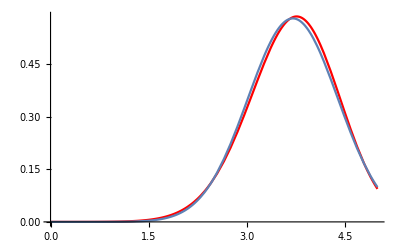

```mathematica
b=2.75;k=2.25;nd=200;ns=300;ndR=4;
beta=betaSolution[b, k, nd, ns, ndR, 1.]//Quiet
(*getSkewNormalParam[b, k, nd, ndR, ns, beta, 1., b+k, 5000]*)
gsList = {g1Int[b, k, nd, ns, ndR, beta, 1.], g21Int[b, k, nd, ns, ndR, beta, 1.],g31Int[b, k, nd, ns, ndR, beta, 1.],g32Int[b, k, nd, ns, ndR, beta, 1.]};
getSkewNormalParam[ns, beta, gsList, b+k, 1200]
getNormalParam[ns, beta, gsList, b+k, 1200]
Show[Plot[puu0SkewNormal[u, b+k, 1200, ns, beta, gsList], {u, 0, 5}, PlotRange->All, PlotStyle->Red],
Plot[puu0Normal[u, b+k, 1200, ns, beta, gsList], {u, 0, 5}, PlotRange->All]]
```

```mathematica
tmpList = Table[{u, puu0SkewNormal[u, b+k, 1200, ns, beta, gsList]}, {u, 1, 8, 0.1}];
Export["tmpList.csv",tmpList,"CSV"];
```

```mathematica
(***************************************************************************************************************************)
(*z=ReLU(u-b)*)
(*expectation value of z with initial overlap u0*)
expzu0SkewNormal[u0_, t_, ns_, b_, beta_, gsList_]:=Module[{mu, sigma, alpha}, 
{mu, sigma, alpha}=getSkewNormalParam[ns, beta, gsList, u0, t];
NIntegrate[PDF[SkewNormalDistribution[mu, sigma, alpha], u](u-b), {u, b, Infinity}]
];

expzu0Normal[u0_, t_, ns_, b_, beta_, gsList_]:=Module[{mu, sigma}, 
{mu, sigma}=getNormalParam[ns, beta, gsList, u0, t];
(ⅇ^((-(b- mu)^2)/(2 sigma^2))sigma)/(√(2. π))-0.5(b-mu) Erfc[(b-mu)/(√2. sigma)]
];
(*expectation value of z^2 with initial overlap u0*)
expz2u0SkewNormal[u0_, t_, ns_, b_, beta_, gsList_]:=Module[{mu, sigma, alpha}, 
{mu, sigma, alpha}=getSkewNormalParam[ns, beta, gsList, u0, t];
NIntegrate[PDF[SkewNormalDistribution[mu, sigma, alpha], u](u-b)^2, {u, b, Infinity}]
];
expz2u0Normal[u0_, t_, ns_, b_, beta_, gsList_]:=Module[{mu, sigma}, 
{mu, sigma}=getNormalParam[ns, beta, gsList, u0, t];
(ⅇ^((-(b-mu)^2)/(2 sigma^2)) sigma(-b+mu))/(√(2. π))+0.5 (sigma^2+(b-mu)^2) Erfc[(b-mu)/(√2. sigma)]
];
(*The probability that z is 0*)
au0SkewNormal[u0_, t_, ns_, b_, beta_, gsList_]:=Module[{mu, sigma, alpha},
{mu, sigma, alpha}=getSkewNormalParam[ns, beta, gsList, u0, t];
NIntegrate[PDF[SkewNormalDistribution[mu, sigma, alpha], u], {u, -Infinity, b}]
];
au0Normal[u0_, t_, ns_, b_, beta_, gsList_]:=Module[{mu, sigma}, 
{mu, sigma}=getNormalParam[ns, beta, gsList, u0, t];
 0.5+0.5*Erf[(b-mu)/(√2. sigma)]
];
(*expectation value of z^3 with initial overlap u0*)
expz3u0SkewNormal[u0_, t_, ns_, b_, beta_, gsList_]:=Module[{mu, sigma, alpha}, 
{mu, sigma, alpha}=getSkewNormalParam[ns, beta, gsList, u0, t];
NIntegrate[PDF[SkewNormalDistribution[mu, sigma, alpha], u](u-b)^3, {u, b, Infinity}]
];
expz3u0Normal[u0_, t_, ns_, b_, beta_, gsList_]:=Module[{mu, sigma, alpha}, 
{mu, sigma, alpha}=getSkewNormalParam[ns, beta, gsList, u0, t];
(ⅇ^(-(b-mu)^2/(2 sigma^2)) ((b-mu)^2 sigma+2 sigma^3))/(√(2. π))-0.5 (b-mu) ((b-mu)^2+3 sigma^2) Erfc[(b-mu)/(√2 sigma)]
];
(*---------------------Part I begins-----------------------------------*)
(*Part I: For the group of dendrites that are not picked for update at time 0.*)
(*the dendrite with overlap v is picked for update*)
pLeftMarginI[v_, nd_, Rnd_, qv_]:=(nd  Exp[-v^2/2])/(√(2 π))(1-qv)^(nd-1)(∏_(m=1)^(Rnd-1) qv/(1-qv)*(nd-m)/(Rnd -m));(*qv should always be q[v]*)
(*although the distribution of u is a skew gaussian, the distribution of YI is still assumed to be a delta function at 0 + the positive part of a gaussian*)
getYIParams[t_, b_, k_, ns_,nd_, ndR_, beta_, gsList_]:=Module[{expzI, expz2I, aI, expYI, expY2I, AI, muOverSigmaYI, sigmaYI, muYI}, 
(*expzI = NIntegrate[pLeftMarginI[v, nd, ndR, q[v]] Exp[-u0^2/2.]/((1-q[v])√(2π)) expzu0SkewNormal[u0, t, ns, b, beta, gsList], {v, -Infinity, b+k}, {u0, -Infinity, v}];*)
expzI =NIntegrate[pLeftMarginI[v, nd, ndR, q[v]] Exp[-u0^2/2.]/((1-q[v])√(2π)) expzu0Normal[u0, t, ns, b, beta, gsList], {v, -Infinity, b+k}, {u0, -Infinity, v}];
(*expz2I:=NIntegrate[pLeftMarginI[v, nd, ndR, q[v]] Exp[-u0^2/2.]/((1-q[v])√(2π)) expz2u0SkewNormal[u0, t, ns, b, beta, gsList], {v, -Infinity, b+k}, {u0, -Infinity, v}];*)
expz2I=NIntegrate[pLeftMarginI[v, nd, ndR, q[v]] Exp[-u0^2/2.]/((1-q[v])√(2π)) expz2u0Normal[u0, t, ns, b, beta, gsList], {v, -Infinity, b+k}, {u0, -Infinity, v}];
(*aI = NIntegrate[pLeftMarginI[v, nd, ndR, q[v]] Exp[-u0^2/2.]/((1-q[v])√(2π)) au0SkewNormal[u0, t, ns, b, beta, gsList], {v, -Infinity, b+k}, {u0, -Infinity, v}];*)
aI = NIntegrate[pLeftMarginI[v, nd, ndR, q[v]] Exp[-u0^2/2.]/((1-q[v])√(2π)) au0Normal[u0, t, ns, b, beta, gsList], {v, -Infinity, b+k}, {u0, -Infinity, v}];
(*--------------------------------------------------------*)
expYI=(nd-ndR)expzI;
expY2I=(nd-ndR)(nd-ndR-1)expzI^2 + (nd-ndR)expz2I;
AI=aI^(nd-ndR);
(*--------------------------------------------------------*)
h[x_]:=x+Exp[-x^2/2.]/(√(π/2.)(1+Erf[x/(√2)]));
muOverSigmaYI = x/.FindRoot[((1-AI)expY2I)/expYI^2 h[x]^2==1+x h[x], {x, 100.}];
sigmaYI=expYI/((1-AI)h[muOverSigmaYI]);
muYI=muOverSigmaYI*sigmaYI;
{muYI, sigmaYI, AI}

];
(*---------------------Part I ends-----------------------------------*)
(*Get the 1% false positive boundary. At steady state, the distribution of u should be a standard gaussian distribution. *)
getThreshold[b_, nd_]:=Module[{expz, expz2, a, expY, expY2, A, muOverSigmaSteady, muSteady, sigmaSteady},
expz=(ⅇ^(-b^2/2))/(√(2. π))-0.5 b Erfc[b/(√2.)];
expz2=-(b ⅇ^(-b^2/2))/(√(2.π))+0.5 (1+b^2) Erfc[b/(√2.)];
a=0.5 (1+Erf[b/(√2)]);
expY=nd expz;
expY2=nd(nd-1)expz^2 + nd expz2;
A=a^nd;
h[x_]:=x+Exp[-x^2/2.]/(√(π/2.)(1+Erf[x/(√2)]));
muOverSigmaSteady= x/.FindRoot[((1-A)expY2)/expY^2 h[x]^2==1+x h[x], {x, 100.}]//Quiet;
sigmaSteady=expY/((1-A)h[muOverSigmaSteady]);
muSteady=muOverSigmaSteady*sigmaSteady;
muSteady-√2 sigmaSteady InverseErf[(0.01(1+Erf[muSteady/(√2 sigmaSteady)]))/(1-A)-1]//Quiet
 ];
(*---------------------Part II begins-----------------------------------*)
(*Part II: For the group of dendrites that are picked for update at time 0.*)
(*the dendrite with overlap v is not picked for update*)
pLeftMarginII[v_, nd_, Rnd_, qv_]:=(nd  Exp[-v^2/2])/(√(2 π))(1-qv)^(nd-1)(∏_(m=1)^Rnd qv/(1-qv)*(nd-m)/(Rnd -m+1));(*qv should always be q[v]*)
getYIIParams[t_, b_, k_, ns_,nd_, ndR_, beta_, gsList_]:=Module[{expzII, expz2II, expz3II, expYII, expY2II, expY3II, tmp, muYII, sigmaYII, alphaYII}, 
(*the simple but less accurate version, (not considering the possibility that a dendrite is picked for update but not updated because its overlap is already above b+k)*)
(*&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&*)
expzII = expzu0SkewNormal[b+k, t, ns, b, beta, gsList];
(*expzII = expzu0Normal[b+k, t, ns, b, beta, gsList];*)
expz2II = expz2u0SkewNormal[b+k, t, ns, b, beta, gsList];
(*expz2II = expz2u0Normal[b+k, t, ns, b, beta, gsList];*)
expz3II = expz3u0SkewNormal[b+k, t, ns, b, beta, gsList];
(*expz3II = expz3u0Normal[b+k, t, ns, b, beta, gsList];*)
(*the complex but more accurate version*)
(*&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&*)
(*expzII = NIntegrate[pLeftMarginII[v, nd, ndR, q[v]] Exp[-u0^2/2]/(√(2π) q[v])expzu0SkewNormal[b+k, t, ns, b, beta, gsList], {v, -(b+k), b+k}, {u0, v, b+k}]+NIntegrate[Exp[-u0^2/2]/(√(2π) ndR/nd)expzu0SkewNormal[u0, t, ns, b, beta, gsList], {u0, b+k, Infinity}];
(*expzII =NIntegrate[pLeftMarginII[v, nd, ndR, q[v]] Exp[-u0^2/2]/(√(2π) q[v])expzu0Normal[b+k, t, ns, b, beta, gsList], {v, -(b+k), b+k}, {u0, v, b+k}]+NIntegrate[Exp[-u0^2/2]/(√(2π) ndR/nd)expzu0Normal[u0, t, ns, b, beta, gsList], {u0, b+k, Infinity}];*)
expz2II =NIntegrate[pLeftMarginII[v, nd, ndR, q[v]] Exp[-u0^2/2]/(√(2π) q[v])expz2u0SkewNormal[b+k, t, ns, b, beta, gsList], {v, -(b+k), b+k}, {u0, v, b+k}]+NIntegrate[Exp[-u0^2/2]/(√(2π) ndR/nd)expz2u0SkewNormal[u0, t, ns, b, beta, gsList], {u0, b+k, Infinity}];
(*expz2II = NIntegrate[pLeftMarginII[v, nd, ndR, q[v]] Exp[-u0^2/2]/(√(2π) q[v])expz2u0Normal[b+k, t, ns, b, beta, gsList], {v, -(b+k), b+k}, {u0, v, b+k}]+NIntegrate[Exp[-u0^2/2]/(√(2π) ndR/nd)expz2u0Normal[u0, t, ns, b, beta, gsList], {u0, b+k, Infinity}];*)
expz3II =NIntegrate[pLeftMarginII[v, nd, ndR, q[v]] Exp[-u0^2/2]/(√(2π) q[v])expz3u0SkewNormal[b+k, t, ns, b, beta, gsList], {v, -(b+k), b+k}, {u0, v, b+k}]+NIntegrate[Exp[-u0^2/2]/(√(2π) ndR/nd)expz3u0SkewNormal[u0, t, ns, b, beta, gsList], {u0, b+k, Infinity}];
(*expz3II = NIntegrate[pLeftMarginII[v, nd, ndR, q[v]] Exp[-u0^2/2]/(√(2π) q[v])expz3u0Normal[b+k, t, ns, b, beta, gsList], {v, -(b+k), b+k}, {u0, v, b+k}]+NIntegrate[Exp[-u0^2/2]/(√(2π) ndR/nd)expz3u0Normal[u0, t, ns, b, beta, gsList], {u0, b+k, Infinity}];*)*)

(*&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&*)
expYII = ndR expzII;
expY2II =  ndR expz2II+ndR(ndR-1)expzII^2;
expY3II = ndR expz3II + 3ndR(ndR-1)expzII expz2II +ndR(ndR-1)(ndR-2)expzII^3;
(*--------------------------------------------------------*)
tmp=Sign[expY3II-3expYII expY2II +2 expYII^3] √(π/2.)(Abs[2/(4-π)(expY3II-3expYII expY2II +2 expYII^3)])^(1/3);
muYII=expYII-√(2./π) tmp;
sigmaYII =√(expY2II-expYII^2+2./π tmp^2);
alphaYII = √(tmp^2/(sigmaYII^2-tmp^2))Sign[tmp];
{muYII, sigmaYII, alphaYII}
];
(*---------------------Part II ends-----------------------------------*)
probY[Y_, muI_, sigmaI_, AI_, muII_, sigmaII_, alphaII_]:=AI PDF[SkewNormalDistribution[muII, sigmaII, alphaII], Y] + (1-AI)/(√(π/2.)sigmaI(1+Erf[muI/(√2 sigmaI)]))NIntegrate[Exp[(-(y-muI)^2)/(2 sigmaI^2)]PDF[SkewNormalDistribution[muII, sigmaII, alphaII], Y-y], {y, 0, Infinity}];
falseNegative[th_, muI_, sigmaI_, AI_, muII_, sigmaII_, alphaII_]:=1-NIntegrate[probY[Y, muI, sigmaI, AI, muII, sigmaII, alphaII], {Y, th, Infinity}];
Y99Lower[muI_, sigmaI_, AI_, muII_, sigmaII_, alphaII_]:=th/.FindRoot[falseNegative[th, muI, sigmaI, AI, muII, sigmaII, alphaII]==0.01, {th, -(b+k), b+k}, Method->"Brent"];
Y99Upper[muI_, sigmaI_, AI_, muII_, sigmaII_, alphaII_]:=th/.FindRoot[falseNegative[th, muI, sigmaI, AI, muII, sigmaII, alphaII]==0.99, {th, 0, 5*(b+k)}, Method->"Brent"];
YMean[muI_, sigmaI_, AI_, muII_, sigmaII_, alphaII_]:=(muII+sigmaII √(2./π)alphaII/(√(1+alphaII^2)))+(1-AI)muI+((1-AI)sigmaI Exp[-muI^2/(2 sigmaI^2)])/(1+Erf[muI/(√2 sigmaI)])√(2./π);
(***************************************************************************************************************************)
```

```mathematica
b=2.75;k=2.25;nd=200;ns=300;ndR=4;
beta=betaSolution[b, k, nd, ns, ndR, 1.]//Quiet;
gsList = {g1Int[b, k, nd, ns, ndR, beta, 1.], g21Int[b, k, nd, ns, ndR, beta, 1.],g31Int[b, k, nd, ns, ndR, beta, 1.],g32Int[b, k, nd, ns, ndR, beta, 1.]};
th = getThreshold[b, nd];
Print["beta: ", beta]
Print["th: ", th]
```

beta: 10.0242

th: 1.41071

```mathematica
t=1200;
yIParams = getYIParams[t, b, k, ns, nd, ndR, beta, gsList]//Quiet;
yIIParams = getYIIParams[t, b, k, ns, nd, ndR, beta, gsList]//Quiet;
falseNegative[th, yIParams[[1]], yIParams[[2]], yIParams[[3]], yIIParams[[1]], yIIParams[[2]], yIIParams[[3]]]//Quiet
Y99Lower[yIParams[[1]], yIParams[[2]], yIParams[[3]], yIIParams[[1]], yIIParams[[2]], yIIParams[[3]]]//Quiet
```

0.0172956

1.16045

```mathematica
ndList={400}; bList={2.5, 2.75, 3.0};kList={2.0, 2.25, 2.5, 2.75, 3.0};ndRList={2, 3, 4};
paramList = Table[{nd, 60000/nd, b, k, ndR}, {nd, ndList}, {b, bList}, {k, kList}, {ndR, ndRList}];
paramList = ArrayReshape[paramList, {Length[ndList]*Length[bList]*Length[kList]*Length[ndRList],5}];
tmpFun[nd_, ns_, b_, k_, ndR_]:={nd, ns, b, k, ndR, betaSolution[b, k, nd, ns, ndR, 1.]}
betaList = MapThread[tmpFun, Transpose[paramList]]//Quiet;
```

```mathematica
Export["beta_list.txt", betaList,"Table","FieldSeparators"->" " ]
```

beta_list.txt

```mathematica
tStart=500; tEnd=1200;tStep=100;
tList=Table[t, {t, tStart, tEnd, tStep}];
f1List=Thread[f1Int[b, k, nd, ndR, ns, beta, 1., tList]];
f2List=Thread[f2Int[b, k, nd, ndR, ns, beta, 1., tList]];
expYIList=Thread[expYI[b, k, f1List, f2List, nd, ndR]];
expY2IList=Thread[expY2I[b, k, f1List, f2List, nd, ndR]];
AIList=Thread[AI[b, k, f1List, f2List, nd, ndR]];
expYIIList=Thread[expYII[b, f1List, f2List, k, ns,nd, ndR]];
expY2IIList=Thread[expY2II[b, f1List, f2List, k, ns, nd, ndR]];
AIIList=Thread[AII[b, f1List, f2List, k, ns, nd, ndR]];
muOverSigmaIList=MapThread[ansatzMuOverSigma, {expYIList,expY2IList, AIList}]//Quiet;
sigmaIList=Thread[ansatzSigma[expYIList,expY2IList, AIList, muOverSigmaIList]];
muIList=Thread[ansatzMu[sigmaIList, muOverSigmaIList]];
muOverSigmaIIList=MapThread[ansatzMuOverSigma, {expYIIList,expY2IIList, AIIList}]//Quiet;
sigmaIIList=Thread[ansatzSigma[expYIIList,expY2IList, AIIList, muOverSigmaIIList]];
muIIList=Thread[ansatzMu[sigmaIIList, muOverSigmaIIList]];
falseNegativeList=Thread[falseNegative[th, muIList, sigmaIList, AIList, muIIList, sigmaIIList, AIIList]];
Y99LowerList=MapThread[Y99Lower,{ muIList, sigmaIList, AIList, muIIList, sigmaIIList, AIIList}]//Quiet;
Y99UpperList=MapThread[Y99Upper,{ muIList, sigmaIList, AIList, muIIList, sigmaIIList, AIIList}]//Quiet;
YMeanList=MapThread[YMean,{ muIList, sigmaIList, AIList, muIIList, sigmaIIList, AIIList}]//Quiet;
```

```mathematica
Y99LowerList
```

{4.41302,3.80166,3.22962,2.69744,2.20699,1.76096,1.36369,1.02176}

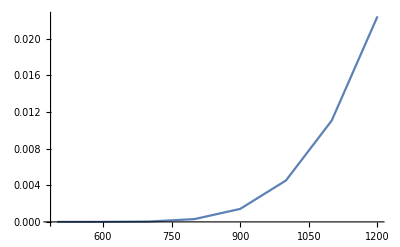

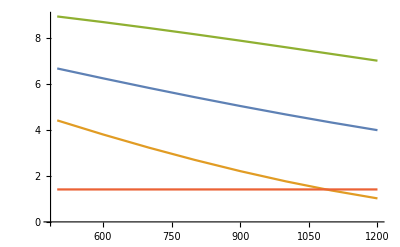

```mathematica
fnTimeList=Transpose[{tList, falseNegativeList}];
meanTimeList=Transpose[{tList, YMeanList}];
lower99TimeList= Transpose[{tList, Y99LowerList}];
upper99TimeList=Transpose[{tList, Y99UpperList}];
ListLinePlot[fnTimeList, PlotRange->All]
ListLinePlot[{meanTimeList, lower99TimeList,upper99TimeList, Table[{t, th}, {t, tList}]}, PlotRange->All]
```

```mathematica
Export["meanTimeList.csv",meanTimeList,"CSV"];
Export["lower99TimeList.csv",lower99TimeList,"CSV"];
Export["upper99TimeList.csv",upper99TimeList,"CSV"];
```

900

0.169999

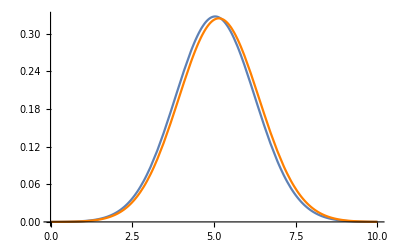

```mathematica
tmpFun1[Y_, mu_, sigma_, A_]:=(1-A)/(√(π/2)sigma(1+Erf[mu/(√2 sigma)]))Exp[(-(Y-mu)^2)/(2 sigma^2)];
tmpFun2[Y_, muI_, sigmaI_, AI_, muII_, sigmaII_, AII_]:=((1-AI)(1-AII)ⅇ^(-(muI+muII-Y)^2/(2 (sigmaI^2+sigmaII^2))))/(√(π/2)√(sigmaI^2+sigmaII^2))((Erf[(muII sigmaI^2+sigmaII^2 (-muI+Y))/(√2 sigmaI sigmaII √(sigmaI^2+sigmaII^2))]+Erf[(muI sigmaII^2+sigmaI^2 (-muII+Y))/(√2 sigmaI sigmaII √(sigmaI^2+sigmaII^2))])/((1+Erf[muI/(√2 sigmaI)])(1+Erf[muII/(√2 sigmaII)])));
idx=5;
tList[[idx]]
(1-AIList[[idx]])(1-AIIList[[idx]])
(*Plot[probY[Y, muIList[[idx]], sigmaIList[[idx]], AIList[[idx]], muIIList[[idx]], sigmaIIList[[idx]], AIIList[[idx]]], {Y, 0, 10}, PlotRange->All]*)
Show[Plot[probY[Y, muIList[[idx]], sigmaIList[[idx]], AIList[[idx]], muIIList[[idx]], sigmaIIList[[idx]], AIIList[[idx]]], {Y, 0, 10}, PlotRange->All],
(*Plot[tmpFun1[Y, muIList[[idx]], sigmaIList[[idx]], AIList[[idx]]], {Y, 0, 10}, PlotRange->All, PlotStyle->Red],Plot[tmpFun1[Y, muIIList[[idx]], sigmaIIList[[idx]], AIIList[[idx]]], {Y, 0, 10}, PlotRange->All, PlotStyle->Green],
Plot[tmpFun2[Y, muIList[[idx]], sigmaIList[[idx]], AIList[[idx]], muIIList[[idx]], sigmaIIList[[idx]], AIIList[[idx]]], {Y, 0, 10}, PlotRange->All],*)
Plot[probY[Y, muIList[[idx]], sigmaIList[[idx]], AIList[[idx]]*0.4, muIIList[[idx]], sigmaIIList[[idx]], AIIList[[idx]]], {Y, 0, 10}, PlotRange->All, PlotStyle->Orange]
]
```

```mathematica
tList[[8]]
```

1200

```mathematica
idx=8;
(*YProbList= Table[{Y, probY[Y, muIList[[idx]], sigmaIList[[idx]], AIList[[idx]], muIIList[[idx]], sigmaIIList[[idx]], AIIList[[idx]]]}, {Y, 0.1, 8, 0.1}];
Export["YProbList.csv",YProbList,"CSV"];*)
```

```mathematica
Print["<zI>: ", expzI[b, k, f1List[[idx]], f2List[[idx]], nd, ndR]]; 
Print["<zII>: ", expzII[b, f1List[[idx]], f2List[[idx]], k, ns, nd, ndR]]
Print["<zI^2>-<zI>^2: ",expz2I[b, k, f1List[[idx]], f2List[[idx]], nd, ndR]-expzI[b, k, f1List[[idx]], f2List[[idx]], nd, ndR]^2]
Print["<zII^2>-<zII>^2: ",expz2II[b, f1List[[idx]], f2List[[idx]], k, ns, nd, ndR]-expzII[b, f1List[[idx]], f2List[[idx]], k, ns, nd, ndR]^2]
Print["<YI>: ",expYIList[[idx]]]
Print["<YII>: ",expYIIList[[idx]]]
Print["<Y>: ",YMeanList[[idx]]]
Print["<YI^2> - <YI>^2: ",expY2IList[[idx]] -expYIList[[idx]]^2]
Print["<YII^2> - <YII>^2: ",expY2IIList[[idx]]-expYIIList[[idx]]^2]
Print["<Y^2>-<Y>^2: ",NIntegrate[Y^2probY[Y, muIList[[idx]], sigmaIList[[idx]], AIList[[idx]], muIIList[[idx]], sigmaIIList[[idx]], AIIList[[idx]]], {Y, 0.00001, Infinity}]-YMeanList[[idx]]^2]
Print["<AI>: ", AIList[[idx]]]
Print["<AII>: ", AIIList[[idx]]]
```

<zI>: 0.000296249

<zII>: 0.982237

<zI^2>-<zI>^2: 0.000128817

<zII^2>-<zII>^2: 0.409348

<YI>: 0.0580648

<YII>: 3.92895

<Y>: 3.98701

<YI^2> - <YI>^2: 0.0252482

<YII^2> - <YII>^2: 1.63739

<Y^2>-<Y>^2: 1.66264

<AI>: 0.779948

<AII>: 0.0000459314

```mathematica
AIvar = 0.773475;
muoversigmaI = ansatzMuOverSigma[0.05999762619336446, 0.029942617847189625, AIvar];
sigmaI = ansatzSigma[0.05999762619336446, 0.029942617847189625, AIvar, muoversigmaI];
muI = sigmaI*muoversigmaI;
AIIvar = 2.5000000000052758*10^(-05);
muoversigmaII = ansatzMuOverSigma[4.192797122399012,19.175944877158138, AIIvar];
sigmaII = ansatzSigma[4.192797122399012,19.175944877158138, AIIvar, muoversigmaII];
muII = sigmaII*muoversigmaII;
Y99Lower[muI, sigmaI, AIvar, muII, sigmaII, AIIvar]
Y99LowerList[[idx]]
falseNegative[th, muI, sigmaI, AIvar, muII, sigmaII, AIIvar]
falseNegativeList[[idx]]
```

General::munfl: Exp[-5000.] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::inumr: The integrand ⅇ^(-0.198582 (1.24299-Y)^2) (Erf[0.36815 (-4.73094+0.912936 (-4.19078+Y))]+Erf[0.36815 (3.82591+1.60491 (2.94779+Y))]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.+th}}.

1.30619

1.02176

0.0125018

0.0224244

```mathematica
AIvar = 0.8050333333333333;
(*AIvar=0.4;
*)muoversigmaI = ansatzMuOverSigma[0.04912103275060654, 0.0231622883472743, AIvar];
sigmaI = ansatzSigma[0.04912103275060654, 0.0231622883472743, AIvar, muoversigmaI];
muI = sigmaI*muoversigmaI;
AIIvar = 3.333333333332966*10^(-05);
muoversigmaII = ansatzMuOverSigma[3.9697947942952316,17.28457665445197, AIIvar];
sigmaII = ansatzSigma[3.9697947942952316,17.28457665445197, AIIvar, muoversigmaII];
muII = sigmaII*muoversigmaII;
Y99Lower[muI, sigmaI, AIvar, muII, sigmaII, AIIvar]
falseNegative[th, muI, sigmaI, AIvar, muII, sigmaII, AIIvar]
```

General::munfl: Exp[-5000.] is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::inumr: The integrand ⅇ^(-0.221385 (1.573-Y)^2) (Erf[0.446729 (-3.67848+0.721951 (-3.96697+Y))]+Erf[0.446729 (2.86396+1.53656 (2.39397+Y))]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.+th}}.

1.14712

0.0176291

```mathematica
AIvar
muI
sigmaI
```

0.773475

-2.94779

0.955477

```mathematica
falseNegative2[th_, muI_, sigmaI_, AI_, muII_, sigmaII_, AII_]:=AI*AII + AI(1-AII)(Erf[muII/(√2 sigmaII)]-Erf[(muII-th)/(√2 sigmaII)])/(1+Erf[muII/(√2 sigmaII)])+AII(1-AI)(Erf[muI/(√2 sigmaI)]-Erf[(muI-th)/(√2 sigmaI)])/(1+Erf[muI/(√2 sigmaI)])+((1-AI)(1-AII))/(√(π/2)√(sigmaI^2+sigmaII^2)(1+Erf[muI/(√2 sigmaI)])(1+Erf[muII/(√2 sigmaII)]))NIntegrate[ⅇ^(-(muI+muII-Y)^2/(2 (sigmaI^2+sigmaII^2)))(Erf[(muII sigmaI^2+sigmaII^2 (-muI+Y))/(√2 sigmaI sigmaII √(sigmaI^2+sigmaII^2))]+Erf[(muI sigmaII^2+sigmaI^2 (-muII+Y))/(√2 sigmaI sigmaII √(sigmaI^2+sigmaII^2))]), {Y, 0, th}];
```

```mathematica
falseNegative2[th, muI, sigmaI, AIvar, muII, sigmaII, AIIvar]
```

0.0176291

```mathematica
falseNegative2[th, muI, sigmaI, AIvar, muII, sigmaII, AIIvar]
```

0.0113751

```mathematica
NIntegrate[(1-AIIvar)/(√(π/2)sigmaII(1+Erf[muII/(√2 sigmaII)]))Exp[(-(Y-muII)^2)/(2 sigmaII^2)], {Y, 0., 2.}]
```

0.0414257

```mathematica
NIntegrate[(1-AIvar)/(√(π/2)sigmaI(1+Erf[muI/(√2 sigmaI)]))Exp[(-(Y-muI)^2)/(2 sigmaI^2)], {Y, 0.1, Infinity}]
```

0.158514

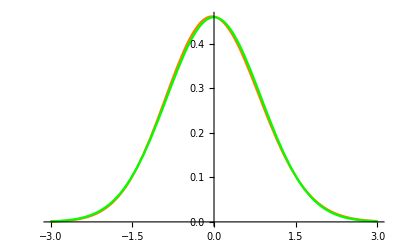

```mathematica
a=0.8;
Show[Plot[PDF[SkewNormalDistribution[0, 1, a], x+(√(2/π) a)/(√(1+a^2))], {x, -3, 3}, PlotStyle->Orange],Plot[ PDF[SkewNormalDistribution[0, √(1-(2 a^2)/(π (1+a^2))), 0], x], {x, -3, 3}, PlotStyle->Green]
]
```

```mathematica
Integrate[Exp[-(x-mu)^2/2/sigma^2]/Sqrt[2Pi sigma^2], {x, 0, Infinity}, Assumptions->{mu∈Reals, sigma>0}]
```

1/2 (1+Erf[mu/(√2 sigma)])

```mathematica
Integrate[Exp[-(x-mu)^2/2/sigma^2]x/Sqrt[2Pi sigma^2], {x, 0, Infinity}, Assumptions->{mu∈Reals, sigma>0}]
```

1/2 (mu+ⅇ^(-mu^2/(2 sigma^2)) √(2/π) sigma+mu Erf[mu/(√2 sigma)])

```mathematica
Clear["b"]
Integrate[Exp[-(x)^2/2]/Sqrt[2Pi ], {x, -Infinity, b}, Assumptions->{b∈Reals, sigma>0}]
```

1/2 (1+Erf[b/(√2)])

```mathematica
Integrate[Exp[-(x)^2/2](x-b)^2/Sqrt[2Pi ], {x, b, Infinity}, Assumptions->{b∈Reals, sigma>0}]
```

-(b ⅇ^(-b^2/2))/(√(2 π))+1/2 (1+b^2) Erfc[b/(√2)]

```mathematica
PDF[SkewNormalDistribution[mu, sigma, alpha], x]
```

(ⅇ^(-(-mu+x)^2/(2 sigma^2)) Erfc[-(alpha (-mu+x))/(√2 sigma)])/(√(2 π) sigma)